```mathematica
Clear["Global`*"]
```

1 - 12 Sample spaces, events
Graph a sample space for the experiments:

1.  Drawing 3 screws from a lot of right-handed and left-handed screws.

Assume there are 24 in the lot, 12 of each.

```mathematica
d=MultivariateHypergeometricDistribution[3,{12,12}]
```

MultivariateHypergeometricDistribution[3,{12,12}]

In a draw of three, the probability of getting 1, 2 or 2 left-handed.

```mathematica
Table[Probability[x>n,{x,y}\[Distributed]d],{n,0,2}]
```

{41/46,1/2,5/46}

But as for the entire probability sample space,

```mathematica
arr=Table[R,{n,12}]
```

{R,R,R,R,R,R,R,R,R,R,R,R}

```mathematica
all=Table[L,{n,12}]
```

{L,L,L,L,L,L,L,L,L,L,L,L}

```mathematica
jj=Join[arr,all]
```

{R,R,R,R,R,R,R,R,R,R,R,R,L,L,L,L,L,L,L,L,L,L,L,L}

Assuming the probabilities are vertically stacked rectangles three high, each stack of three a three-screw draw.

```mathematica
let=Permutations[jj,{3}]
```

{{R,R,R},{R,R,L},{R,L,R},{R,L,L},{L,R,R},{L,R,L},{L,L,R},{L,L,L}}

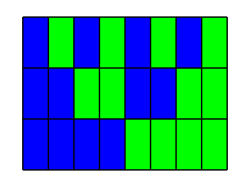

```mathematica
Graphics[{{Blue,Rectangle[{0,0},{1,2}]},{Blue,Rectangle[{0,2},{1,4}]},{Blue,Rectangle[{0,4},{1,6}]},{Blue,Rectangle[{1,0},{2,2}]},{Blue,Rectangle[{1,2},{2,4}]},{Green,Rectangle[{1,4},{2,6}]},{Blue,Rectangle[{2,0},{3,2}]},{Green,Rectangle[{2,2},{3,4}]},{Blue,Rectangle[{2,4},{3,6}]},{Blue,Rectangle[{3,0},{4,2}]},{Green,Rectangle[{3,2},{4,4}]},{Green,Rectangle[{3,4},{4,6}]},{Green,Rectangle[{4,0},{5,2}]},{Blue,Rectangle[{4,2},{5,4}]},{Blue,Rectangle[{4,4},{5,6}]},{Green,Rectangle[{5,0},{6,2}]},{Blue,Rectangle[{5,2},{6,4}]},{Green,Rectangle[{5,4},{6,6}]},{Green,Rectangle[{6,0},{7,2}]},{Green,Rectangle[{6,2},{7,4}]},{Blue,Rectangle[{6,4},{7,6}]},{Green,Rectangle[{7,0},{8,2}]},{Green,Rectangle[{7,2},{8,4}]},{Green,Rectangle[{7,4},{8,6}]},{Table[Line[{{n,0},{n,6}}],{n,0,8}]},{Table[Line[{{0,n},{8,n}}],{n,0,6,2}]}},ImageSize->250]
```

3.  Rolling 2 dice.

A pair of fair dice can be modeled using a DiscreteUniformDistribution.

```mathematica
dice =DiscreteUniformDistribution[{2,12}];
```

Generate a simulation of ten throws.

```mathematica
RandomVariate[dice,10]
```

{3,5,11,6,7,3,5,6,2,4}

Compute the probability that the sum of three dice throws is less than 12:

```mathematica
NProbability[Sum[x[i],{i,3}]≤12,{x[1]\[Distributed]dice,x[2]\[Distributed]dice,x[3]\[Distributed]dice}]
```

0.0631104

As for the sample space, I am kludging it. A serious deficiency of the cell below is that dealing with a single list, the appearance of a double is not possible.

```mathematica
gr=Permutations[{1,2,3,4,5,6},{2}]
```

{{1,2},{1,3},{1,4},{1,5},{1,6},{2,1},{2,3},{2,4},{2,5},{2,6},{3,1},{3,2},{3,4},{3,5},{3,6},{4,1},{4,2},{4,3},{4,5},{4,6},{5,1},{5,2},{5,3},{5,4},{5,6},{6,1},{6,2},{6,3},{6,4},{6,5}}

Since the problem is asking for a plot, maybe the deficiency is minor, since the diagonal can be easily filled in.

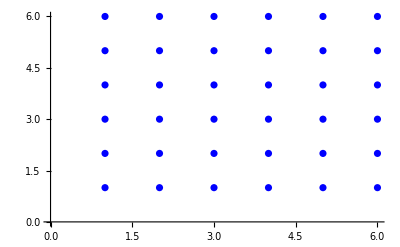

```mathematica
ListPlot[{gr,Range[6]},PlotStyle->Blue]
```

or

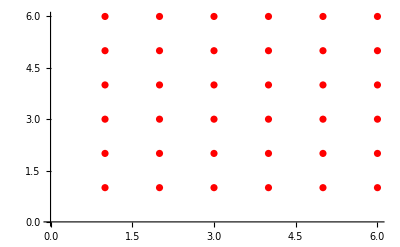

```mathematica
ListPlot[Table[Table[j,{n,1,6}],{j,1,6}],PlotStyle->Red]
```

5.  Tossing a coin until the first Head appears.

```mathematica
heads1=NegativeBinomialDistribution[1,1/2]
```

NegativeBinomialDistribution[1,1/2]

Plot the distribution of tail counts:

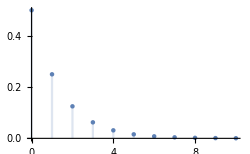

```mathematica
DiscretePlot[PDF[heads1,k],{k,0,10},ImageSize->250]
```

Compute the probability of getting at least 4 tails before getting 1 heads :

```mathematica
NProbability[tails≥4,tails\[Distributed]heads1]
```

0.0625

Compute the expected number of tails before getting the first heads :

```mathematica
Mean[heads1]
```

1

Now to draw something concerning the sample space.

```mathematica
s1=Range[4]
```

{1,2,3,4}

```mathematica
ex=Table[Table[0,{n,m}],{m,0,8}]
```

{{},{0},{0,0},{0,0,0},{0,0,0,0},{0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

```mathematica
ty=Table[Join[ex[[n]],s1],{n,6}]
```

{{1,2,3,4},{0,1,2,3,4},{0,0,1,2,3,4},{0,0,0,1,2,3,4},{0,0,0,0,1,2,3,4},{0,0,0,0,0,1,2,3,4}}

The sample space expands without bound while those coin tails keep showing up. Meanwhile the PDF is hugging the x-axis. I would rather that this plot expanded parallel to the y-axis, right now it seems something of a cheat.

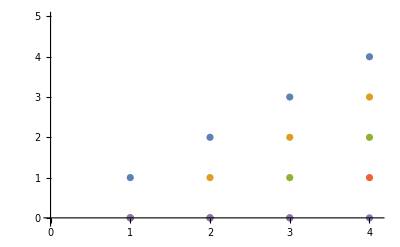

```mathematica
ListPlot[Table[ty[[n]],{n,1,5}],PlotRange->{{0,4.1},{-0.1,5}}]
```

7.  Recording the daily maximum temperature X and the daily maximum air pressure Y at Times Square in New York.

Trying to imitate some summer month.

```mathematica
Clear["Global`*"]
```

```mathematica
ap=NumberForm[RandomReal[{29.0,30.9},30],{4,2}];
```

```mathematica
apo={"29.18","30.65","29.94","29.11","30.60","29.08","29.99","30.46","29.70","29.45","30.79","30.38","30.04","30.01","30.07","29.44","29.79","29.98","29.20","30.69","30.10","30.83","30.09","29.38","30.43","29.36","29.92","29.91","29.89","30.34"};
```

```mathematica
tem=NumberForm[RandomReal[{80,95},30],{4,1}];
```

```mathematica
temo={"86.0","81.9","87.7","85.0","85.6","90.3","87.5","90.6","81.0","94.2","92.0","90.5","82.7","83.3","81.4","83.6","81.6","82.1","85.3","91.8","92.9","81.5","83.3","83.2","88.6","91.4","94.8","83.2","89.2","87.6"};
```

```mathematica
rn=Range[30];
```

```mathematica
rno={1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30};
```

```mathematica
gr1=Grid[Table[{rno[[n]],apo[[n]],temo[[n]]},{n,1,30}],Frame->All];
```

```mathematica
gr2=Grid[{{"D "," Barom "," Temp  "}},Frame->All];
```

```mathematica
Column[{gr2,gr1}]
```

D  |  Barom  |  Temp  
1 | 29.1823 | 86.0422
2 | 30.6537 | 81.8799
3 | 29.9417 | 87.6654
4 | 29.1096 | 84.9861
5 | 30.602 | 85.6174
6 | 29.0788 | 90.2995
7 | 29.9908 | 87.516
8 | 30.4619 | 90.6359
9 | 29.7044 | 80.9539
10 | 29.4492 | 94.1649
11 | 30.7925 | 92.0376
12 | 30.3816 | 90.5361
13 | 30.0417 | 82.7174
14 | 30.0127 | 83.2556
15 | 30.0736 | 81.4441
16 | 29.4426 | 83.6029
17 | 29.7918 | 81.5751
18 | 29.9754 | 82.0692
19 | 29.1969 | 85.3386
20 | 30.6868 | 91.8394
21 | 30.1033 | 92.8817
22 | 30.8257 | 81.4626
23 | 30.0897 | 83.3201
24 | 29.383 | 83.166
25 | 30.4293 | 88.5701
26 | 29.3594 | 91.4326
27 | 29.9168 | 94.8236
28 | 29.9136 | 83.238
29 | 29.892 | 89.1724
30 | 30.3383 | 87.5693

I don’t know what the plot of a legitimate sample space for this problem would be. Maybe something along the lines of brackets, with random values inside, would do. How about this: A plot based on the record high (and low) temperature for the date, bracketed with some sufficient cushion to catch the possible heat/cold wave. And then another dataset for the humidity percentage, similarly bracketed. The two plotted datasets could be shown together using the transparent filling style shown in the 5th example under basic plotting in the Mathematica documentation. And any point with double-valued coordinate inside the combined area would be in the sample universe.

9.  Drawing gaskets from a lot of 10, containing one defective D, until D is drawn, one at a time, and assuming sampling without replacement, that is, gaskets drawn are not returned to the lot. (More about this in section 24.6).

I’m going to pull out one gasket from a box with changing number of good gaskets and one remaining bad gasket.

```mathematica
di[n_]=MultivariateHypergeometricDistribution[1,{n,1}]
```

MultivariateHypergeometricDistribution[1,{n,1}]

I want to get a table of probabilities for my chances of not getting the bad gasket on the next pull.

```mathematica
Table[Probability[x==1&&y==0,{x,y}\[Distributed]di[n]],{n,9,1,-1}]
```

{9/10,8/9,7/8,6/7,5/6,4/5,3/4,2/3,1/2}

I notice I have to paste the Out line to get a list I can calculate with.

```mathematica
dip={9/10,8/9,7/8,6/7,5/6,4/5,3/4,2/3,1/2};
```

I assemble a list of accumulating probabilities for avoiding the bad gasket. I feel sure I could save some space by using a loop, but not smart enough yet.

```mathematica
dip2=dip[[1]] dip[[2]];
```

```mathematica
dip3=dip2 dip[[3]];
```

```mathematica
dip4=dip3 dip[[4]];
```

```mathematica
dip5=dip4 dip[[5]];
```

```mathematica
dip6 =dip5 dip[[6]];
```

```mathematica
dip7=dip6 dip[[7]];
```

```mathematica
dip8=dip7 dip[[8]];
```

```mathematica
dip9=dip8 dip[[9]];
```

The accumulated probabilities look familiar.

```mathematica
ndip=N[{9/10,dip2,dip3,dip4,dip5,dip6,dip7,dip8,dip9}]
```

{0.9,0.8,0.7,0.6,0.5,0.4,0.3,0.2,0.1}

10. In rolling 3 dice, are the events A: Sum Divisible by 3 and B: Sum divisible by 5 mutually exclusive?

11. Answer the questions in problem 10 for rolling 2 dice.

Yes. There are only 11 number results, therefore no common multiples of 3 and 5.

17.  Using a Venn diagram, show that A ⊂ B if and only if A ∪ B = B.

```mathematica
Clear["Global`*"]
```

```mathematica
disk1= ImplicitRegion[(x-2)^2+(y)^2<4,{x,y}];
disk2= ImplicitRegion[(x-0.5)^2+y^2<1,{x,y}];
disk3= ImplicitRegion[(x-2.9)^2+y^2<0.6, {x,y}];
```

I make three disks for the attempt at explaining. Left an orange, middle a blue, and right a green.

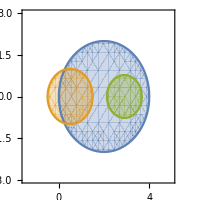

```mathematica
RegionPlot[{(x-2)^2+(y)^2<4,(x-0.5)^2+y^2<1,(x-2.9)^2+y^2<0.6},{x,-3,6},{y,-6,6},AspectRatio->Automatic,ImageSize->200,PlotRange->{{-1.5,5},{-3,3}},Epilog->{Blue,Text[Style["A",Bold,Large],{6,0}]}]
```

```mathematica
r2=BooleanRegion[Xor,{disk1,disk2}];
r3=BooleanRegion[And,{disk1,disk2}];
r4=BooleanRegion[Or,{disk1,disk2}];
r5=BooleanRegion[Xor,{disk1,disk3}];
r6=BooleanRegion[And,{disk1,disk3}];
r7=BooleanRegion[Or,{disk1,disk3}];
```

```mathematica
p1=RegionPlot[r2,AspectRatio->Automatic,ImageSize->200,PlotRange->{{-1.5,5},{-3,3}}];
p2=RegionPlot[r3,AspectRatio->Automatic,ImageSize->200,PlotRange->{{-1.5,5},{-3,3}}];
p3=RegionPlot[r4,AspectRatio->Automatic,ImageSize->200,PlotRange->{{-1.5,5},{-3,3}}];
p4=RegionPlot[r5,AspectRatio->Automatic,ImageSize->200,PlotRange->{{-1.5,5},{-3,3}}];
p5=RegionPlot[r6,AspectRatio->Automatic,ImageSize->200,PlotRange->{{-1.5,5},{-3,3}}];
p6=RegionPlot[r7,AspectRatio->Automatic,ImageSize->200,PlotRange->{{-1.5,5},{-3,3}}];
```

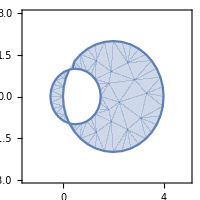
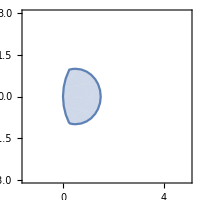
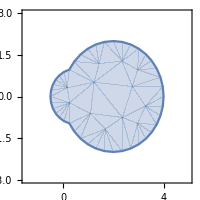

```mathematica
Row[{p1,p2,p3}]
```

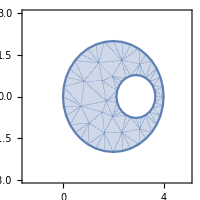
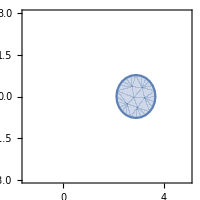
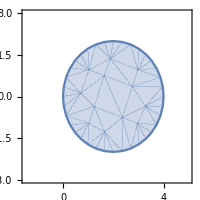

```mathematica
Row[{p4,p5,p6}]
```

The if and only if goes two ways. Boolean operations appeal to logic. XOR between a parent set and a subset should be total destruction of the subset, since its reliance on the parent for points is total.  Left, below is displayed such total destruction, whereas in left, above a surviving crescent exists. AND between a parent set and a subset should deflate the parent to the exact boundaries of the subset, demonstrating that all points inventoried in the subset are also in the parent. Middle, below is seen the total extent of the candidate, whereas middle, above shows deficits. OR between a parent set and a subset should reveal the parent totally, with total dissolution of the subset. This is basically the right-pointed arrow of the iff, and seen below right. The bump seen above right is an unauthorized augmentation of the candidate parent, which refutes a subset relation. To get the left-pointed iff arrow seems a little slippery, and I think of it as a combination of the two left panels.